# GHZ STATES - Cirq Amplitude damping

## N = 2

Ideal case

```mathematica
rho=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
sigma=({{0, 0, 0, -1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {-1, 0, 0, 0}})
```

{{0,0,0,-1},{0,0,1,0},{0,1,0,0},{-1,0,0,0}}

```mathematica
{{0,0,0,-1},{0,0,1,0},{0,1,0,0},{-1,0,0,0}}
```

{{0,0,0,-1},{0,0,1,0},{0,1,0,0},{-1,0,0,0}}

```mathematica
R=sigma.rho.sigma
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
R//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
R=R.R
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Eigenvalues[R]
```

{0,0,0,0}

```mathematica
Concurrence=Max[0,Eigenvalues[R][[1]]-Eigenvalues[R][[2]]-Eigenvalues[R][[3]]-Eigenvalues[R][[4]]]
```

0

Ideal case

```mathematica
rho=({{0.5, 0, 0, 0.5}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0.5, 0, 0, 0.5}});
```

```mathematica
sigma=({{0, 0, 0, -1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {-1, 0, 0, 0}});
```

```mathematica
{{0,0,0,-1},{0,0,1,0},{0,1,0,0},{-1,0,0,0}}
```

{{0,0,0,-1},{0,0,1,0},{0,1,0,0},{-1,0,0,0}}

```mathematica
R=Sqrt[Sqrt[rho].sigma.rho.sigma.Sqrt[rho]]
```

{{1.,0.,0.,1.},{0.,0.,0.,0.},{0.,0.,0.,0.},{1.,0.,0.,1.}}

```mathematica
R//MatrixForm
```

(1. | 0. | 0. | 1.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
1. | 0. | 0. | 1.)

```mathematica
Eigenvalues[R]
```

{2.,0.,0.,0.}

```mathematica
Concurrence=Max[0,Eigenvalues[R][[1]]-Eigenvalues[R][[2]]-Eigenvalues[R][[3]]-Eigenvalues[R][[4]]]
```

2.

Non-Ideal case

```mathematica
rho={{0.495263010263443,0.0,0.0,0.4764038920402527},{0.0,0.009582798928022385,0.0031780966091901064,0.0},{0.0,0.0031780966091901064,0.019456148147583008,0.0},{0.4764038920402527,0.0,0.0,0.4756961464881897}};
```

```mathematica
sigma=({{0, 0, 0, -1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {-1, 0, 0, 0}})
```

{{0,0,0,-1},{0,0,1,0},{0,1,0,0},{-1,0,0,0}}

```mathematica
{{0,0,0,-1},{0,0,1,0},{0,1,0,0},{-1,0,0,0}}
```

{{0,0,0,-1},{0,0,1,0},{0,1,0,0},{-1,0,0,0}}

```mathematica
R=sigma.rho.sigma
```

{{0.475696,0.,0.,0.476404},{0.,0.0194561,0.0031781,0.},{0.,0.0031781,0.0095828,0.},{0.476404,0.,0.,0.495263}}

```mathematica
R//MatrixForm
```

(0.475696 | 0. | 0. | 0.476404
0. | 0.0194561 | 0.0031781 | 0.
0. | 0.0031781 | 0.0095828 | 0.
0.476404 | 0. | 0. | 0.495263)

```mathematica
Eigenvalues[R]
```

{0.961984,0.0203907,0.00897524,0.00864827}

```mathematica
Concurrence=Max[0,Eigenvalues[R][[1]]-Eigenvalues[R][[2]]-Eigenvalues[R][[3]]-Eigenvalues[R][[4]]]
```

0.92397

Plot 1 (gamma e p hanno gli stessi valori)

```mathematica
(*gamma e p hanno gli stessi valori *)
```

```mathematica
data={0.9999999403953553,0.9239697284160725,0.8524003341860014,0.785081039445694,0.7218093305168201,0.662392175976906,0.6066566550454903,0.5544262219776611,0.5055395340106896,0.45984670151694673,0.4171966150811013,0.37745070264073516,0.34047276235466295,0.30613082821621257,0.27430098574943595,0.24485651836336653,0.2176794974343887,0.19265192691244137,0.1696576400401253,0.14858355439081583,0.1293175963991165,0.11175035844837061,0.09577455384011468,0.08128433828211223,0.06817785094520779,0.05635540856457631,0.04572109542483771,0.036182288146872965,0.02765107541139726,0.02004241471217255,0.013278625528726912,0.007283016572646517,0.001986550363094919,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0};
```

```mathematica
gamma=Drop[Table[i,{i,0,0.1,0.001}],-1];
Cdata=Thread[{gamma,data}];
k=0.1
y=1.01
```

0.1

1.01

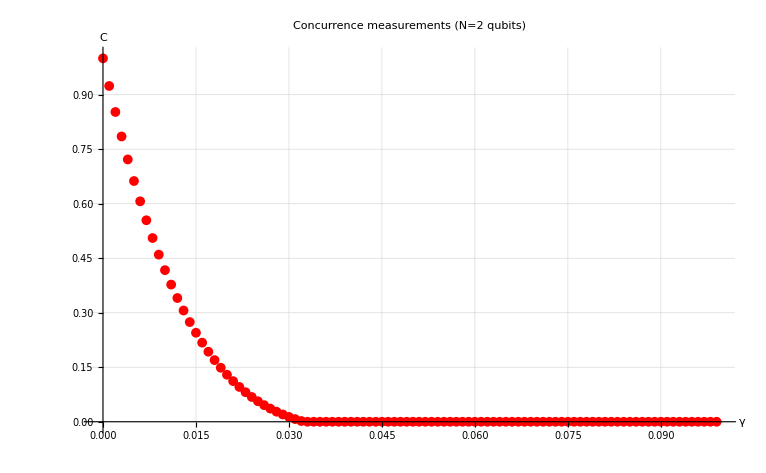

```mathematica
PlotC=ListPlot[Cdata,AxesLabel->{Style["γ",Black,FontFamily->"HoldForm",FontSize->16],Style["C",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Concurrence measurements (N=2 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-0.001,k},{-0.01,y}}, PlotLegends->{},PlotStyle->{Red}]
```

Plot 2 (gamma varia, p è fissato a 0.01) inutile

```mathematica
(*gamma varia, p è fissato a 0.01*)
```

```mathematica
data={0.550796777009964,0.5338052145938746,0.5176833641378089,0.5024077328501337,0.4879543828129721,0.47429950699676415,0.46142128274547806,0.44929524354665173,0.43789724377965444,0.4272062817616379,0.4171966150811013,0.40784668587065587,0.39913295597216825,0.3910319676175419,0.38352244229145627,0.3765805006261084,0.3701844121014914,0.36431239778983704,0.3589431623654491,0.3540547233886712,0.3496274038691139,0.34563992473170535,0.3420733028801739,0.33890779472053345,0.3361243239112456,0.33370530241210106,0.33163255938907277,0.3298890366570871,0.3284584396322978,0.32732456940057464,0.32647131655599365,0.32588568446178,0.3255518031308178,0.3254558765453667,0.32558613867886255,0.32592880486804526,0.32647247343496233,0.32720514418574875,0.32811607809657717,0.32919558517752723,0.3304318101458745,0.3318161938276196,0.3333408790724981,0.33499535094637894,0.33677228249590474,0.3386637031876496,0.340662186661179,0.34276029172737843,0.3449519438911704,0.34723031493625645,0.3495898630804378,0.3520238326187118,0.35452837953575034,0.3570970254567389,0.3597251622765396,0.36240855645313674,0.36514263384146695,0.36792281916914826,0.3707452652323333,0.3736074361796159,0.3765039867883764,0.37943249967281006,0.3823899899084343,0.385373429086431,0.38837946025659287,0.39140654676682796,0.39445027609572614,0.3975095680892067,0.40058163904387956,0.40366536397255004,0.4067574767996427,0.4098569320396317,0.41296114244367804,0.41606875580836267,0.41917816911010086,0.4222880873578385,0.4253974346111465,0.4285033690332347,0.4316061315911389,0.43470358550184096,0.4377945769930953,0.4408791196229614,0.44395499163298835,0.44702193834080806,0.4500785365674127,0.4531247732914154,0.45615908205434935,0.4591808118797495,0.46218959840915236,0.4651842205257881,0.4681650786646869,0.47113096917035246,0.4740811671774952,0.47701516094998064,0.4799325573155291,0.48283345649131526,0.4857168327403849,0.48858317929736195,0.49143113796698357,0.4942607032004695};
```

```mathematica
gamma=Drop[Table[i,{i,0,0.1,0.001}],-1];
Cdata=Thread[{gamma,data}];
k=0.1
y=1.01
```

0.1

1.01

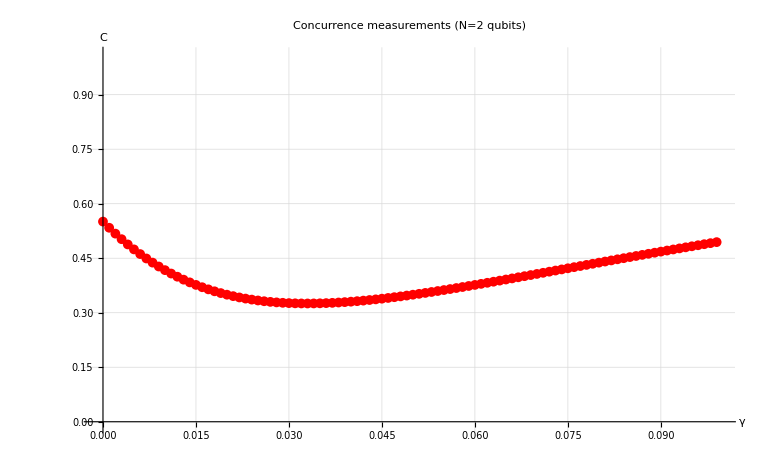

```mathematica
PlotC=ListPlot[Cdata,AxesLabel->{Style["γ",Black,FontFamily->"HoldForm",FontSize->16],Style["C",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Concurrence measurements (N=2 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-0.001,k},{-0.01,y}}, PlotLegends->{},PlotStyle->{Red}]
```

Plot 3 (gamma varia, p è fissato a 0.001) inutile

```mathematica
(*gamma varia, p è fissato a 0.01*)
```

```mathematica
data={0.9475969187915325,0.9239697284160725,0.9013026831515039,0.8795733232114451,0.8587562540039103,0.8388270581789661,0.8197639760428617,0.8015415745563268,0.784137261170206,0.7675311150351501,0.7516980019732166,0.7366166518673659,0.722265918267276,0.7086233297874228,0.6956696928382815,0.6833814322257555,0.6717399414644384,0.6607237411066549,0.6503144716194826,0.6404910261896388,0.6312340152073413,0.6225256316585062,0.6143460122835144,0.6066771335401718,0.5995012555981247,0.5928001052893404,0.586557522231093,0.5807561645129375,0.5753782007275015,0.5704095773027745,0.5658333402892806,0.561634787040699,0.5577985175122877,0.5543100219137072,0.551155632872651,0.5483209890624736,0.5457933752108872,0.5435592257018845,0.5416068341416924,0.5399231717932402,0.5384970880077463,0.5373169579384249,0.5363715251942311,0.5356508639876385,0.5351448970578062,0.534842347576606,0.5347359863300336,0.5348141382126913,0.5350693537494183,0.5354931910218521,0.536077178154551,0.5368134342937174,0.537693921542401,0.5387129650668175,0.5398616050895544,0.5411338189184682,0.542524012362932,0.5440249598006193,0.5456316144032569,0.5473371348461624,0.5491367674268184,0.5510260777413325,0.5529982566673355,0.5550501399418258,0.5571759635514357,0.5593718422032492,0.5616342178585401,0.5639572593792952,0.5663389255907069,0.568774388952649,0.5712609548219019,0.5737942715295052,0.5763721355358908,0.5789906452831637,0.5816472754855121,0.5843385247689762,0.5870625923278431,0.5898160658882852,0.5925976359425944,0.5954030616022301,0.598232098233155,0.6010813053596786,0.6039487928920503,0.6068335416228641,0.6097320090103702,0.6126436274554337,0.6155665053870417,0.6184987069671353,0.6214383641369322,0.6243848300369299,0.6273361395663493,0.6302916125608138,0.6332488139531458,0.6362070006435199,0.6391659641045329,0.6421227865107113,0.6450774455427355,0.6480284961505154,0.6509764989564655,0.653918209092939};
```

```mathematica
gamma=Drop[Table[i,{i,0,0.1,0.001}],-1];
Cdata=Thread[{gamma,data}];
k=0.1
y=1.01
```

0.1

1.01

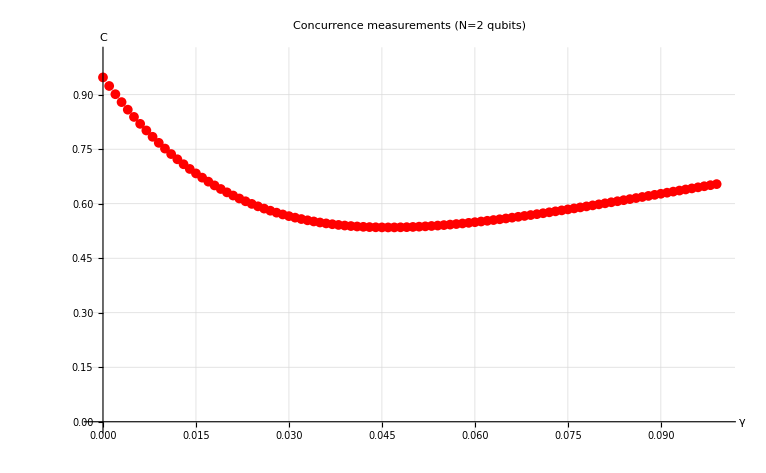

```mathematica
PlotC=ListPlot[Cdata,AxesLabel->{Style["γ",Black,FontFamily->"HoldForm",FontSize->16],Style["C",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Concurrence measurements (N=2 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-0.001,k},{-0.01,y}}, PlotLegends->{},PlotStyle->{Red}]
```

```mathematica
(*gamma varia, p è fissato a 0.01*)
```

```mathematica
data2={0.550796777009964,0.5338052145938746,0.5176833641378089,0.5024077328501337,0.4879543828129721,0.47429950699676415,0.46142128274547806,0.44929524354665173,0.43789724377965444,0.4272062817616379,0.4171966150811013,0.40784668587065587,0.39913295597216825,0.3910319676175419,0.38352244229145627,0.3765805006261084,0.3701844121014914,0.36431239778983704,0.3589431623654491,0.3540547233886712,0.3496274038691139,0.34563992473170535,0.3420733028801739,0.33890779472053345,0.3361243239112456,0.33370530241210106,0.33163255938907277,0.3298890366570871,0.3284584396322978,0.32732456940057464,0.32647131655599365,0.32588568446178,0.3255518031308178,0.3254558765453667,0.32558613867886255,0.32592880486804526,0.32647247343496233,0.32720514418574875,0.32811607809657717,0.32919558517752723,0.3304318101458745,0.3318161938276196,0.3333408790724981,0.33499535094637894,0.33677228249590474,0.3386637031876496,0.340662186661179,0.34276029172737843,0.3449519438911704,0.34723031493625645,0.3495898630804378,0.3520238326187118,0.35452837953575034,0.3570970254567389,0.3597251622765396,0.36240855645313674,0.36514263384146695,0.36792281916914826,0.3707452652323333,0.3736074361796159,0.3765039867883764,0.37943249967281006,0.3823899899084343,0.385373429086431,0.38837946025659287,0.39140654676682796,0.39445027609572614,0.3975095680892067,0.40058163904387956,0.40366536397255004,0.4067574767996427,0.4098569320396317,0.41296114244367804,0.41606875580836267,0.41917816911010086,0.4222880873578385,0.4253974346111465,0.4285033690332347,0.4316061315911389,0.43470358550184096,0.4377945769930953,0.4408791196229614,0.44395499163298835,0.44702193834080806,0.4500785365674127,0.4531247732914154,0.45615908205434935,0.4591808118797495,0.46218959840915236,0.4651842205257881,0.4681650786646869,0.47113096917035246,0.4740811671774952,0.47701516094998064,0.4799325573155291,0.48283345649131526,0.4857168327403849,0.48858317929736195,0.49143113796698357,0.4942607032004695};
```

Plot 4 (gamma varia, p è fissato a 0.001)

```mathematica
(*gamma varia fino a 0.5, p è fissato a 0.01*)
```

```mathematica
data={0.9475969187915325,0.9239697284160725,0.9013026831515039,0.8795733232114451,0.8587562540039103,0.8388270581789661,0.8197639760428617,0.8015415745563268,0.784137261170206,0.7675311150351501,0.7516980019732166,0.7366166518673659,0.722265918267276,0.7086233297874228,0.6956696928382815,0.6833814322257555,0.6717399414644384,0.6607237411066549,0.6503144716194826,0.6404910261896388,0.6312340152073413,0.6225256316585062,0.6143460122835144,0.6066771335401718,0.5995012555981247,0.5928001052893404,0.586557522231093,0.5807561645129375,0.5753782007275015,0.5704095773027745,0.5658333402892806,0.561634787040699,0.5577985175122877,0.5543100219137072,0.551155632872651,0.5483209890624736,0.5457933752108872,0.5435592257018845,0.5416068341416924,0.5399231717932402,0.5384970880077463,0.5373169579384249,0.5363715251942311,0.5356508639876385,0.5351448970578062,0.534842347576606,0.5347359863300336,0.5348141382126913,0.5350693537494183,0.5354931910218521,0.536077178154551,0.5368134342937174,0.537693921542401,0.5387129650668175,0.5398616050895544,0.5411338189184682,0.542524012362932,0.5440249598006193,0.5456316144032569,0.5473371348461624,0.5491367674268184,0.5510260777413325,0.5529982566673355,0.5550501399418258,0.5571759635514357,0.5593718422032492,0.5616342178585401,0.5639572593792952,0.5663389255907069,0.568774388952649,0.5712609548219019,0.5737942715295052,0.5763721355358908,0.5789906452831637,0.5816472754855121,0.5843385247689762,0.5870625923278431,0.5898160658882852,0.5925976359425944,0.5954030616022301,0.598232098233155,0.6010813053596786,0.6039487928920503,0.6068335416228641,0.6097320090103702,0.6126436274554337,0.6155665053870417,0.6184987069671353,0.6214383641369322,0.6243848300369299,0.6273361395663493,0.6302916125608138,0.6332488139531458,0.6362070006435199,0.6391659641045329,0.6421227865107113,0.6450774455427355,0.6480284961505154,0.6509764989564655,0.653918209092939,0.656854167016858,0.6597831155166619,0.6627048289589649,0.6656177885424458,0.6685223088745971,0.67141653622857,0.6742997773669519,0.6771726810292704,0.6800332527115582,0.6828821105949113,0.6857186770896841,0.6885411246723803,0.6913508170422806,0.6941458539096632,0.6969271585303234,0.6996926497231031,0.7024427832829953,0.7051785273075541,0.7078977134917683,0.7106002682433789,0.7132866905054436,0.7159567835324946,0.7186092809888012,0.7212451488457665,0.7238630174504361,0.726463959083054,0.7290462938303071,0.7316113385296554,0.7341583690131226,0.7366862969029797,0.7391969675330556,0.7416881923972583,0.7441612368286402,0.7466157742562277,0.7490507421019985,0.7514680567814472,0.7538651250689034,0.7562444838186273,0.7586040249072947,0.7609449955431706,0.7632668851131387,0.7655699189216928,0.7678530718696436,0.7701172690730889,0.7723626917514073,0.7745889195638018,0.7767968636329985,0.778985043903226,0.781154084150387,0.7833040316708153,0.7854356222055935,0.7875477968899074,0.7896411235847927,0.7917162829509885,0.7937718527574541,0.7958088481028134,0.7978272764200085,0.7998273321257863,0.8018096601628417,0.8037717197095491,0.8057164085688706,0.8076431280276517,0.8095508583108103,0.8114416180369365,0.8133131869545365,0.8151680866502108,0.8170037175907798,0.8188225451908167,0.8206235588410182,0.8224071507074344,0.8241728318515086,0.8259215418829347,0.8276530829798161,0.829366929246435,0.8310642978175328,0.8327446234259384,0.8344082284927388,0.8360550759161609,0.8376847478686303,0.8392988052681604,0.8408959489343562,0.8424770242003216,0.8440420283693754,0.8455908068045711,0.8471238004979358,0.8486403891276305,0.8501425865230268,0.851628362488162,0.8530984350655946,0.8545537423528398,0.8559939433517085,0.8574180097760854,0.8588282324673328,0.8602230590424924,0.8616036190693843,0.8629684133013267,0.8643201104390634,0.8656564296118043,0.8669789416722367,0.8682871718156339,0.8695814483322977,0.8708616194505057,0.872128376007475,0.8733812032191981,0.874619966985488,0.8758457364690639,0.8770585357852148,0.8782577264593795,0.8794433535027149,0.88061671100417,0.8817770451617921,0.8829250104976576,0.8840598993350779,0.885181793373637,0.8862916543093615,0.8873887381078419,0.8884752751621043,0.8895482449361801,0.8906096120187712,0.891658956711967,0.8926967131935745,0.8937227366810623,0.8947372535663298,0.8957400366147596,0.8967315551326605,0.8977125125971019,0.8986816870214724,0.8996399467132169,0.900587649099273,0.9015248011014845,0.9024500994239617,0.903365528844591,0.9042712502394138,0.9051650843131605,0.906049854242776,0.9069236755529113,0.9077880275865446,0.9086419447305673,0.9094863964489379,0.9103206150753215,0.9111455841520186,0.9119607713039495,0.9127660832967676,0.9135625670921417,0.9143494667100354,0.9151269872736755,0.9158957695850816,0.9166553816242657,0.9174061963004563,0.9181482025599955,0.9188809086091088,0.9196053877695074,0.9203212490499818,0.9210285000841141,0.9217275620075815,0.9224178461413605,0.9231006570041033,0.923774623610335,0.9244411356855274,0.9250990797853322,0.9257491711036938,0.9263920394685594,0.9270268284751653,0.9276540372659695,0.9282738188383624,0.9288854470547987,0.9294908329737253,0.9300875518810465,0.9306776340521016,0.9312605023445442,0.9318364175882607,0.9324056410068979,0.9329674796213099,0.9335224404065848,0.9340703968059998,0.9346116432644842,0.9351467724199911,0.9356750801568213,0.9361965854567613,0.9367121675499268,0.9372210219345583,0.9377235623909427,0.9382199137528223,0.9387100352265041,0.9391943331075558,0.9396724200117745,0.9401444972530189,0.9406106265077572,0.9410712195965862,0.9415257997087129,0.9419743912838521,0.9424178642500627,0.9428559300949741,0.9432883113976507,0.9437149598617934,0.9441359295902145,0.9445516267765841,0.9449624706554473,0.9453688394724613,0.9457684925251457,0.946163551562864,0.946553884384294,0.9469397593232936,0.9473200905711119,0.9476955637334983,0.9480656889799137,0.9484314890177972,0.9487930868659387,0.9491488640327599,0.949501499035659,0.9498485463495369,0.9501910733381485,0.9505295513343149,0.9508634421344018,0.9511935448906521,0.9515188966947115,0.9518403414118661,0.952157033482242,0.9524698353691621,0.9527787620568919,0.9530833293231415,0.9533837924420314,0.9536804103663838,0.9539738034236198,0.9542623307136938,0.9545470241888826,0.9548287090599663,0.9551063069144264,0.9553802760351285,0.9556507058738548,0.9559168104742909,0.9561800334150103,0.9564397843003096,0.9566960538663665,0.9569494251734114,0.9571981883745129,0.9574445134949496,0.9576866720300089,0.9579261374055859,0.9581622521320272,0.9583957464104473,0.9586251227298326,0.9588516663473592,0.9590756846471644,0.9592959762569783,0.9595139177057459,0.9597284734114087,0.9599394273363059,0.9601489588074257,0.9603545942806138,0.9605580939770956,0.9607578765493727,0.960955741339887,0.9611503379653508,0.9613428101183126,0.9615323010169674,0.9617189783211326,0.961903052546342,0.9620852445509577,0.9622641033731263,0.9624408602373878,0.9626147812951977,0.9627871201255592,0.9629560755767442,0.9631229980890144,0.9632876716180978,0.9634500533445217,0.9636097968377622,0.9637679452021342,0.9639230102027506,0.964076385117867,0.9642279377146963,0.9643767068951759,0.9645235122338013,0.9646687970643704,0.9648113786173909,0.9649521658862006,0.9650906988104122,0.965227109654569,0.9653617523369191,0.9654950645922475,0.9656257109208048,0.9657548573502557,0.965881596787109,0.966007220059633,0.9661307567395867,0.9662519721492275,0.9663723452372349,0.9664901232694372,0.9666067479438741,0.9667214388233257,0.9668344585521169,0.9669457549865399,0.9670552908841828,0.9671634108434465,0.9672700198796913,0.9673746597929055,0.9674785040566464,0.9675805785175972,0.9676808273048656,0.9677795540384382,0.9678766581441138,0.9679728511584235,0.9680673694054741,0.9681605816969769,0.9682522160941905,0.9683422036858885,0.9684317999009299,0.968518827315185,0.968605666395129,0.9686903110785468,0.968774193745282,0.9688564184682562,0.9689375533616462,0.9690177576857033,0.969096461477515,0.9691737439044825,0.9692505381562229,0.9693256167554576,0.9693997080011209,0.9694727494989257,0.9695442187815211,0.9696146550897446,0.9696846591298237,0.9697529419563298,0.9698207515453396,0.9698873158340724,0.9699521794100852,0.970016237277818,0.97008002867659,0.9701420141335513,0.9702037480295522,0.9702645234938181,0.9703232704404546,0.9703816764284499,0.9704397870957667,0.9704966236255186,0.9705519336318595,0.9706068579875996,0.9706612858680304,0.970713680593691,0.9707659439275392,0.9708174984520701,0.9708685723435977,0.970918289229848,0.9709676074439049,0.9710155751762383,0.9710628629811909,0.9711102876307529,0.971155450039812,0.9712007073876245,0.9712453593214952,0.9712891087513401,0.9713323812931859,0.9713747178066722,0.9714162160823472,0.9714572076725325,0.9714973247064136,0.9715368680024854,0.9715762631766299,0.9716146152293005,0.9716518338235636,0.9716891464437978,0.9717256739225865,0.9717614786599872,0.9717968111827915,0.9718315588021745,0.9718654123201302,0.9718987414727631,0.9719319122708305,0.9719643240122859,0.9719961685506315,0.9720276796486491,0.9720584587012562,0.9720886109487351,0.9721182714337335,0.9721476217649448,0.9721765380772694,0.9722044410888314,0.9722323953020702,0.9722599303998047,0.9722864708254302,0.9723125949308649,0.9723383083047231,0.9723643289973218,0.9723891864509666,0.9724139945279724,0.9724379522915989,0.972461744264386,0.9724849718409109,0.9725081761199873,0.9725305282251,0.9725526251344937,0.9725740486847642,0.9725959285706824,0.9726167430115906,0.972637654298451,0.9726580272697101,0.9726778703076584,0.9726971172887482};
```

```mathematica
k=0.5
y=1.01
```

0.5

1.01

```mathematica
gamma=Drop[Table[i,{i,0,k,0.001}],-1];
Cdata=Thread[{gamma,data}];
```

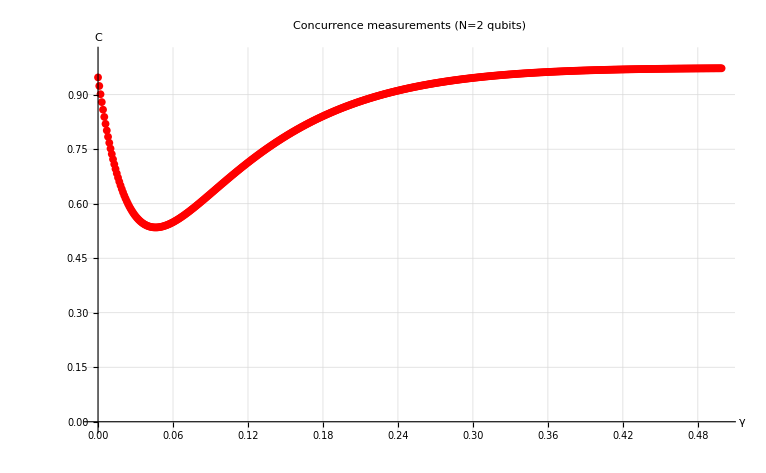

```mathematica
PlotC=ListPlot[Cdata,AxesLabel->{Style["γ",Black,FontFamily->"HoldForm",FontSize->16],Style["C",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Concurrence measurements (N=2 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-0.001,k},{-0.01,y}}, PlotLegends->{},PlotStyle->{Red}]
```

Plot 5 (gamma fissato a 0.001, p varia)

```mathematica
(*gamma fissato a 0.001,p varia*)
```

```mathematica
data={0.9754952874583275,0.9239697284160725,0.8742337899927168,0.8262260446753427,0.7798876918676635,0.7351577528263171,0.6919870933769143,0.6503162000302698,0.6100936154223002,0.5712741339531514,0.5338052145938746,0.49764224659206735,0.4627394506239777,0.4290526332042679,0.39654185094073285,0.3651635212787618,0.33488060155681637,0.30565458373006454,0.2774488768748187,0.2502286214116301,0.22395837075217945,0.1986075461639507,0.17414123197718684,0.15053111753753115,0.12774593724132607,0.10575776460931488,0.0845397244809605,0.06406343367466305,0.04430383421227238,0.025236239990759496,0.006835942340649576,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0};
```

```mathematica
k=0.5
y=1.01
```

0.5

1.01

```mathematica
gamma=Drop[Table[i,{i,0,k,0.001}],-1];
Cdata=Thread[{gamma,data}];
```

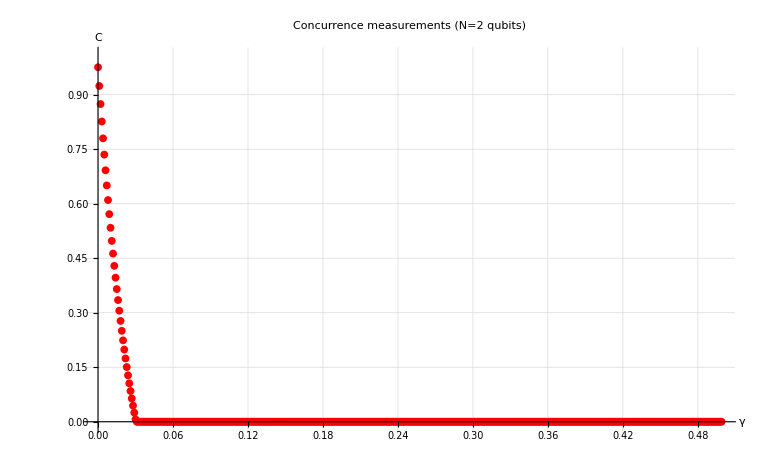

```mathematica
PlotC=ListPlot[Cdata,AxesLabel->{Style["γ",Black,FontFamily->"HoldForm",FontSize->16],Style["C",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Concurrence measurements (N=2 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-0.001,k},{-0.01,y}}, PlotLegends->{},PlotStyle->{Red}]
```

Plot Amplitude

```mathematica
(*gamma fissato a 0.001,p varia*)
```

```mathematica
data={0.999999880790714,0.9751380715039173,0.9505551785814594,0.9262557256253263,0.9022435969814283,0.8785226328170475,0.8550968297146169,0.8319704000793311,0.8091465377263553,0.7866295443030614,0.7644225693179556,0.7425290886243587,0.7209528257472679,0.699696354077209,0.6787634674877391,0.6581567106189246,0.6378786185160008,0.617932199283886,0.598319577169448,0.5790429962722954,0.560104894412633,0.5415066819459906,0.5232502276960354,0.5053368888705232,0.48776836346682295,0.47054520780535236,0.4536687882584278,0.43713959973355687,0.4209581547183992,0.40512475903595657,0.3896396569516605,0.3745026623632297,0.3597134674316046,0.34527160843285815,0.3311764920330982,0.31742713626293656,0.3040225850745888,0.29096136393533656,0.2782423726007264,0.2658638924415464,0.25382389607049327,0.2421206186921389,0.2307519187137076,0.21971535699837808,0.20900858408026035,0.19862877217834857,0.1885733495135733,0.17883907601276305,0.16942294682063386,0.1603216924713194,0.15153183016125307,0.14304986010127185,0.1348720361875343,0.12699453003719793,0.11941338494697294,0.11212441855482475,0.10512343564054225,0.09840611822201348,0.09196800572136171,0.08580443258858692,0.07991075408392634,0.07428217317812522,0.068913775405473,0.06380047466008121,0.058937249858003554,0.054318807561960294,0.049939872389845194,0.04579504023118444,0.041878804545460946,0.03818557855004304,0.03470967845568959,0.031445355882092935,0.028386771025519886,0.02552799417241198,0.02286301270899215,0.020385739763944734,0.018089994953983425,0.015969535796921057,0.014018038738738416,0.012229081942691983,0.010596194808045358,0.009112803506518535,0.007772266206093496,0.006567861543813768,0.005492787838661695,0.004540157579863601,0.0037030087542140756,0.002974292305809166,0.0023468750326015343,0.001813539534487241,0.0013669796003425907,0.0009998006486687367,0.0007045152812655241,0.00047354372216208213,0.0002992105088820237,0.00017374079357947056,8.925903832472667 10^-05,3.7785763703558094 10^-05,1.1234636041490167 10^-05,1.4092428210756593 10^-06,0.0};
```

```mathematica
k=1.01
y=1.01
```

1.01

1.01

```mathematica
gamma=Drop[Table[i,{i,0,k,0.01}],-1];
Cdata=Thread[{gamma,data}];
verticalSize=430;
orSize=600;
```

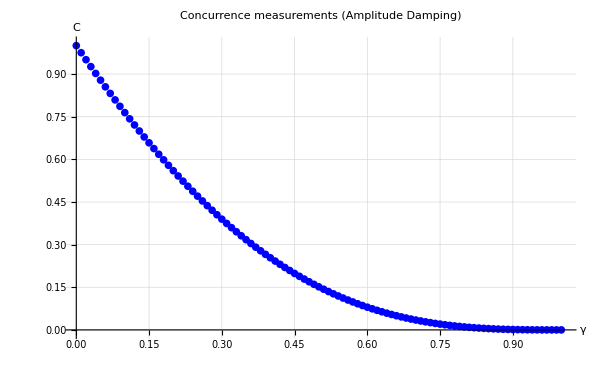

```mathematica
PlotC=ListPlot[Cdata,AxesLabel->{Style["γ",Black,FontFamily->"HoldForm",FontSize->16],Style["C",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Concurrence measurements (Amplitude Damping)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-0.001,k},{-0.01,y}}, PlotLegends->{},PlotStyle->{Blue},ImageSize->{orSize,verticalSize}]
```

Plot Depolarizing

```mathematica
(*gamma fissato a 0.001,p varia*)
```

```mathematica
data={0.999999880790714,0.9103075381547816,0.8275405633717972,0.7511896616762636,0.680777882594492,0.6158600610018811,0.556020729604776,0.5008734623716321,0.4500578147362527,0.4032401083485698,0.3601104028591493,0.32038041272390094,0.28378468347750974,0.2500764658861938,0.21902950910084718,0.1904331488920279,0.16409399613929798,0.13983395063937898,0.11748856370395354,0.09690706647903591,0.07795056354159946,0.06049126810032668,0.044412046784136586,0.029604973698018955,0.015971513361315706,0.003420666887385855,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0};
```

```mathematica
k=1.01
y=1.01
```

1.01

1.01

```mathematica
gamma=Drop[Table[i,{i,0,k,0.01}],-1];
Cdata=Thread[{gamma,data}];
```

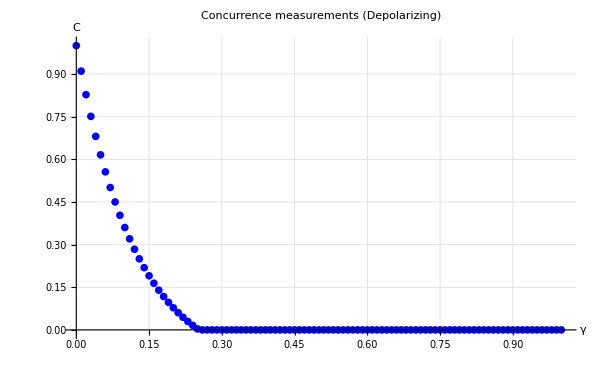

```mathematica
PlotC=ListPlot[Cdata,AxesLabel->{Style["γ",Black,FontFamily->"HoldForm",FontSize->16],Style["C",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Concurrence measurements (Depolarizing)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-0.001,k},{-0.01,y}}, PlotLegends->{},PlotStyle->{Blue},ImageSize->{orSize,verticalSize}]
```